-0.3

9.56366

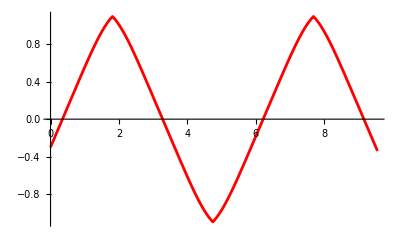

12.0396

```mathematica
f[y_]:=1.4-0.18*y^4;
n[y_,w_]:=f[y]*(1-(0.35*10^14/w)^2);
startAngle=-40 Degree;
y0=-0.3
length=8+2*Sin[17.951958020513104*y0]
radius=1.1;
delta=radius/1000;

calculate[a_,w_,delta_]:=(
dist=0;
xPrev=0;
yPrev=-0.3;
x=0;
y=-0.3;
angle=a;
points=List[];
dchange=0;
direction=1;
AppendTo[points,{x,y}];
While[
x<length,

If[Abs[y-direction*radius]<delta,direction*=-1;dchange=1,];
If[(n[y,w]/n[y+direction*delta,w])*Sin[angle]>1,direction*=-1;dchange=1,];
If[dchange==0,angle=ArcSin[(n[y,w]/n[y+direction*delta,w])*Sin[angle]],];
xPrev=x;
yPrev=y;
x+=Tan[angle]*delta;
y+=direction*delta;
dist+=Sqrt[((x-xPrev)^2+(Abs[y]-Abs[yPrev])^2)];
AppendTo[points,{x,y}];
dchange=0;
];
{points,angle, dist}
);

w=3.1*10^14;
angle=90 Degree-ArcSin[f[0]/n[0,w]*Sin[startAngle]];
results=calculate[angle,w,delta];
points=results[[1]];
plot=ListLinePlot[points,PlotStyle->{Red}];

Show[plot]
Print[results[[3]]];
```

```mathematica
-0.3
```

-0.3